Problem 1a

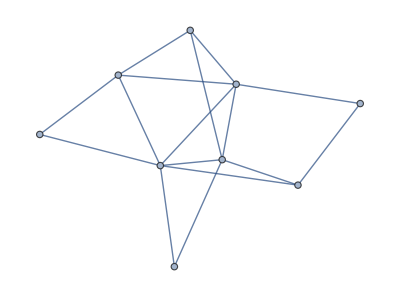
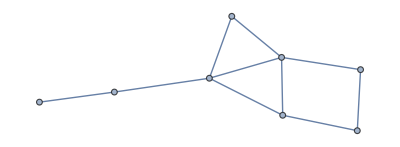
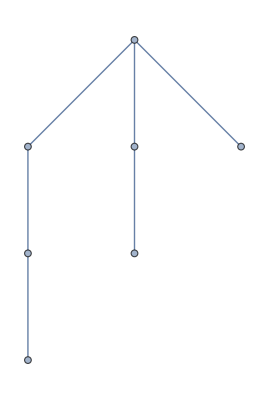
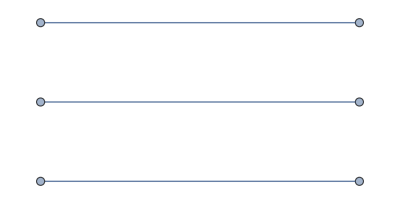

```mathematica
seqs={
{6,5,5,4,3,3,2,2,2},
{4, 4,3,2,2,2,2,1},
{3,2,2,2,1,1,1},
{1,1,1,1, 1, 1}
};
Map[Function[i, RandomGraph[DegreeGraphDistribution[i]]],seqs]
```

Problem 1b

{{4,3,2,2,2,1,1,1,0},{2,1,1,1,1,1,1,0},{1,1,1,1},{1,1}}

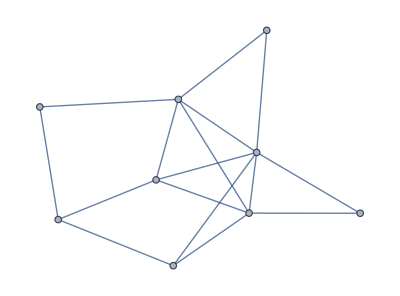
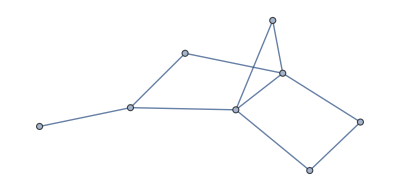
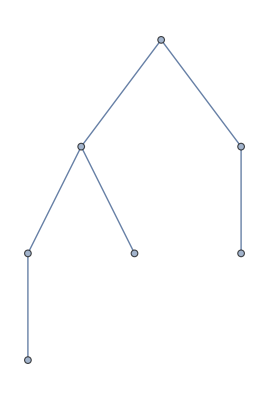
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
seqsb={
{4,3,2,2,2,1,1,1,0},
{2,1,1,1,1,1,1,0},
{1,1,1,1},
{1,1}
}
Map[Function[i, RandomGraph[DegreeGraphDistribution[i]]],seqs]
```

Problem 2a

```mathematica
p2Seqs:={
{6,5,5,3,2,1},
{5,5,5,3,2,1},
{5,5,4,3,2,1},
{5,5,3,3,2,1},
{5,5,3,2,2,1},
{5,5,3,2,1,1}
};
Map[Function[i, GraphQ[i]],p2Seqs]
```

{False,False,False,False,False,False}

Problem 2b

```mathematica
p2bBaseSeq={7,7,5,5,4,3,2};
p2bSeqs = Map[Function[i, Reverse[Sort[Join[p2bBaseSeq, {i}]]]],Range[0,7]]
```

{{7,7,5,5,4,3,2,0},{7,7,5,5,4,3,2,1},{7,7,5,5,4,3,2,2},{7,7,5,5,4,3,3,2},{7,7,5,5,4,4,3,2},{7,7,5,5,5,4,3,2},{7,7,6,5,5,4,3,2},{7,7,7,5,5,4,3,2}}

```mathematica
Map[Function[i, GraphQ[i]],p2bSeqs]
```

{False,False,False,False,False,False,False,False}

Problem 3a

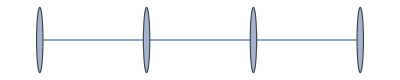

```mathematica
graph3a = Graph[{1<->2,2<->3,3<->4}]
```

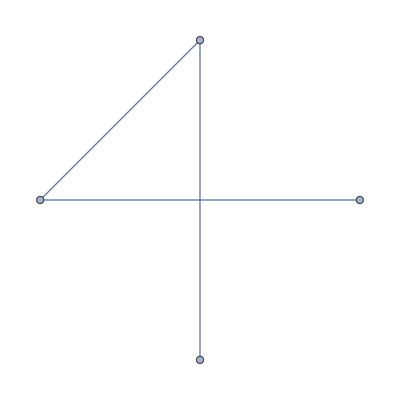

```mathematica
graph3aComplement=GraphComplement[graph3a]
```

```mathematica
IsomorphicGraphQ[graph3a, graph3aComplement]
```

True

Problem 3b

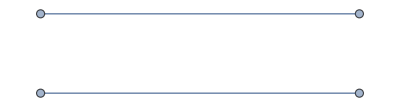

```mathematica
graph3b =Graph[{1<->2,3<->4}]
```

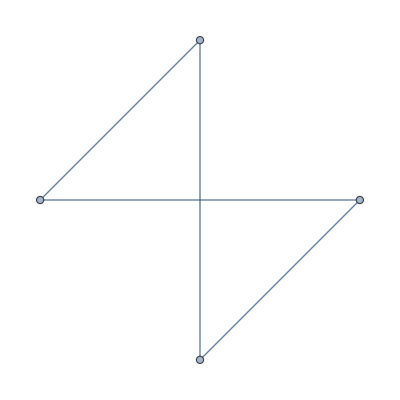

```mathematica
graph3bComplement = GraphComplement[graph3b]
```

```mathematica
IsomorphicGraphQ[graph3b, graph3bComplement]
```

False

Problem 3c

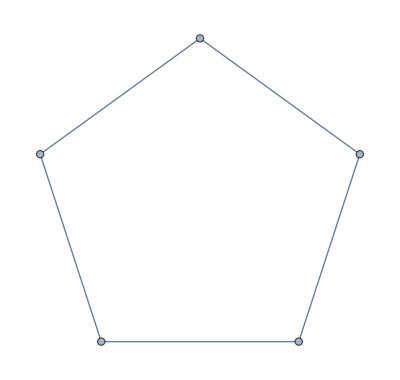

```mathematica
graph3c =Graph[{1<->2,2<->3,3<->4,4<->5,5<->1}]
```

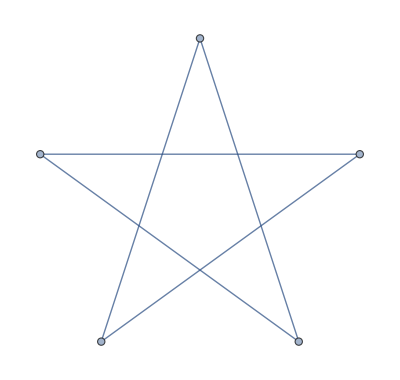

```mathematica
graph3cComplement =GraphComplement[graph3c]
```

```mathematica
IsomorphicGraphQ[graph3c, graph3cComplement]
```

True

Problem 4

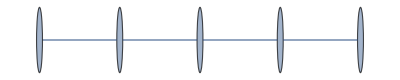

```mathematica
graph3d =Graph[{1<->2,2<->3,3<->4,4<->5}]
```

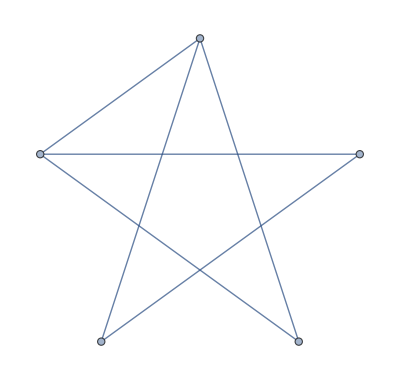

```mathematica
graph3dComplement = GraphComplement[graph3d]
```

```mathematica
IsomorphicGraphQ[graph3d, graph3dComplement]
```

False

Problem 4

```mathematica
mat4 = {
{0,1,1,1,1,1},
{1,0,0,0,0,0},
{1,0,0,0,0,0},
{1,0,0,0,0,0},
{1,0,0,0,0,0},
{1,0,0,0,0,0}
};
mat4 //MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
mat4.mat4//MatrixForm
```

(5 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1)

```mathematica
mat4 + mat4.mat4 //MatrixForm
```

(5 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1)

```mathematica
k=2
```

2